```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)
(*Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)Import["C:\\Users\\KitKa\\QuESTlink\\Rydberg Custom Gates Custom SWAP.wl"];(*Configuration File*)data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

Import::nffil: File /Users/questuser/Documents/QuESTlink/Link/QuESTlink.m not found during Import.

$Failed

CreateLocalQuESTEnv::error: Local quest_link executable not found!

Import::nffil: File /Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl not found during Import.

Import::nffil: File /Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv not found during Import.

CreateRydbergDevice[<|NQubits→9,QubitLocations→<|0→{0,0,0},1→{0,1,0},2→{1,0,0},3→{1,1,0},4→{0,2,0},5→{1,2,0},6→{2,0,0},7→{2,1,0},8→{2,2,0}|>,BlockadeRadius→10,UnitLattice→1,VacuumLifeTime→4000000,LeakProbInit→0.007,DurInit→300,FidMeas→100,DurMeas→20000,AtomLossMeas→0,T2→1.49×10^6,LeakProbCZ→<|1→0.001,11→0.001|>,Ω→1,FidSWAP→99.7|>][InitLocations]

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]

(*This is Incorrect, and has NOT been implemented*)
MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

```mathematica
(*Single qubit gates transpiled using Qiskit procedure into x,y rotations*)
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
HXTrans[q_]:=Subscript[Ry, q][Pi/2]
XHTrans[q_]:=Subscript[Ry, q][-Pi/2]
XHXTrans[q_]:={Subscript[Ry, q][-Pi/2],Subscript[Rx, q][-Pi]}
HXHTrans[q_]:={Subscript[Ry, q][-Pi],Subscript[Rx, q][-Pi]}
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}

(*Native Rydberg CCZ gate decomposed into ARP CZ and Native Single Qubit Rotations*)
Subscript[CCZDecomp,t_,c1_,c2_]:=Flatten[{XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t], Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t],Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],TGate[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1],TGate[c2],Tdg[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1]}]
(*DrawCircuit[ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2],RydDev,ReplaceAliases->True]]]*)
```

```mathematica
(*(*I hope this hasn't been used subsequently*)
CliffCCZRyd={HXTrans[0],HXTrans[0],Table[XTrans[i],{i,1,8}],Subscript[CCZ, 0,6,1],HXTrans[6],Subscript[CCZ, 7,6,2],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,5,4] XHTrans[8],Subscript[CCZ, 8,7,3]}
(*3 Qubit Grover Iteration, this can be neglected*)
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Join[Position[Reverse[SearchSeed][[1]],1],Position[Reverse[SearchSeed][[2;;]],0]]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]*)
```

```mathematica
(*C5X, C5Z, transpiled into native Rydberg gates using ARP CCZ, Ancilla 6,7,8*)
(*C5XTranspiled=Flatten[{Table[XTrans[i],{i,1,8}],XTrans[0],HXTrans[0],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],XHTrans[0],XTrans[0],Table[XTrans[i],{i,1,8}]}];
C5ZCliffTrans=Join[HTrans[0],C5XTranspiled,HTrans[0]];*)

(*Direct ARP CCZ Oracle generation procedure, 6 Data qubits + 3 ancilla.*)
GroverOracle6D3A[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]
(*Direct ARP CCZ Grover Diffusion Operator*)
GroverDiffusion6D3A=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];
```

{0,0,0,0,0,0}

```mathematica
(*Generate empty array for data storage*)
RenormList2Q=Table[{},{i,1,64}]

(*Decomposed CCZ via ARP CZ gate Grover Oracle Generation*)
GroverOracle6D3A2Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]

(*Decomposed CCZ via ARP CZ gate Grover Diffusion Operator*)
GroverDiffusion6D3A2Q=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

(*Decomposed CCZ, Variable Iteration Number Grover Alg Application Routine*)
GroverAlg6D3AVaryIt2Q[SearchSeed_]:=Flatten[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q}]
Init9=Table[Subscript[Init, i],{i,0,8}];
GroverDataUnNormCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroverAlg6D3AVaryIt2Q[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList2Q[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,64}]

(*Variable Iteration Number Decomp CCZ Grover Alg Routine Data Processing*)
RenormDataVaryIt2Q=Table[{j,Mean[RenormList2Q[[All,j]]],StandardDeviation[RenormList2Q[[All,j]]]/8},{j,1,8}]
GroverDataUnnormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]/8},{j,1,8}]
GroverData2ndHighestUnnormVaryIt2Q=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]],{i,1,64}]]/8},{j,1,8}]

GroverDataRenormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]/8},{j,1,8}]
GroverData2ndHighestRenormVaryIt2Q=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]]/RenormList2Q[[All,j]][[i]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]/RenormList2Q[[All,j]][[i]],{i,1,64}]]/8},{j,1,8}]
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,8}]
```

{{1,0.734217,0.0000469948},{2,0.574485,0.000171744},{3,0.451123,0.000370314},{4,0.355585,0.000560409},{5,0.281647,0.000693049},{6,0.223596,0.000741836},{7,0.177656,0.000719813},{8,0.140988,0.000646049}}

{{1,0.0979423±0.000436605},{2,0.195315±0.00107253},{3,0.258081±0.00161728},{4,0.273696±0.00182908},{5,0.247097±0.00162908},{6,0.195319±0.00115516},{7,0.136402±0.000801417},{8,0.0836495±0.00096609}}

{{1,0.0136792±0.0000945766},{2,0.00787351±0.0000582801},{3,0.00527439±0.0000390548},{4,0.00270932±0.0000366665},{5,0.00168208±0.0000508647},{6,0.00105269±0.0000324545},{7,0.00110444±0.0000195017},{8,0.00133829±0.0000222519}}

{{1,0.133399±0.000600386},{2,0.340015±0.00195702},{3,0.572281±0.00401965},{4,0.770283±0.00622863},{5,0.878387±0.00757872},{6,0.874709±0.00704773},{7,0.768289±0.00471901},{8,0.592366±0.0047116}}

{{1,0.0186306±0.00012806},{2,0.0137066±0.000104096},{3,0.0116924±0.0000877937},{4,0.00761274±0.0000936206},{5,0.00595117±0.000168215},{6,0.00469068±0.000134758},{7,0.00621221±0.000102022},{8,0.00954012±0.000194014}}

{{1,0.265783±0.0000469948},{2,0.425515±0.000171744},{3,0.548877±0.000370314},{4,0.644415±0.000560409},{5,0.718353±0.000693049},{6,0.776404±0.000741836},{7,0.822344±0.000719813},{8,0.859012±0.000646049}}

```mathematica
RenormDataVaryIt2Q={{1,0.7342165303021817,3.5813907106676723*^-9},{2,0.5744849340982545,7.812354455277304*^-9},{3,0.451123347756977,1.1529312939099698*^-8},{4,0.3555850135878708,1.4382338013567163*^-8},{5,0.28164688968026624,1.6822226100152315*^-8},{6,0.22359555509350898,1.9897023196452725*^-8},{7,0.17765624753819118,2.438590391602956*^-8},{8,0.14098756136335625,3.029224370795262*^-8}}
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,8}]
```

{{1,0.734217,3.58139×10^-9},{2,0.574485,7.81235×10^-9},{3,0.451123,1.15293×10^-8},{4,0.355585,1.43823×10^-8},{5,0.281647,1.68222×10^-8},{6,0.223596,1.9897×10^-8},{7,0.177656,2.43859×10^-8},{8,0.140988,3.02922×10^-8}}

{{1,0.265783±3.58139×10^-9},{2,0.425515±7.81235×10^-9},{3,0.548877±1.15293×10^-8},{4,0.644415±1.43823×10^-8},{5,0.718353±1.68222×10^-8},{6,0.776404±1.9897×10^-8},{7,0.822344±2.43859×10^-8},{8,0.859012±3.02922×10^-8}}

```mathematica
DestroyAllQuregs[];
```

```mathematica
RenormList=Table[{},{i,1,64}]

(*GroversAlg6D3A[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A},{j,1,8}]]]*)
(*GroverDataUnNormCCZ=Table[If[IntegerQ[i/8],Print[i]];SearchSeed=KetList[6][[i]];
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3A[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
RenormList[[i]]=Renorm;
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,64}];
*)
RenormList=Table[{},{i,1,64}];
Init9=Table[Subscript[Init, i],{i,0,8}];
(*Variable Iteration Direct ARP CCZ Grover Algorithm Applier*)
GroversAlg6D3AVaryIt[SearchSeed_]:=Flatten[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A}]
GroverDataUnNormCCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3AVaryIt[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,64}];

(*Direct ARP CCZ Grover Data Processing*)
RenormDataVaryIt=Table[{j,Mean[RenormList[[All,j]]],StandardDeviation[RenormList[[All,j]]]/8},{j,1,8}]
GroverDataUnnormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]/8},{j,1,8}]
GroverData2ndHighestUnnormVaryIt=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]],{i,1,64}]]/8},{j,1,8}]
GroverDataRenormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]/8},{j,1,8}]
GroverData2ndHighestRenormVaryIt=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]]/RenormList[[All,j]][[i]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]/RenormList[[All,j]][[i]],{i,1,64}]]/8},{j,1,8}]
PLossVaryIt=Table[{i,(1-RenormDataVaryIt[[i,2]])±RenormDataVaryIt[[i,3]]},{i,1,8}]
(*DrawCircuit[GroverOracle6D3A[KetList[6][[1]]]]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]]*)
(*ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]*)
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
(*Total Probability of all output states Direct ARP CCZ*)
RenormDataVaryIt={{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,3.029224370795262*^-8}}
```

{{1,0.851566,3.58139×10^-9},{2,0.771403,7.81235×10^-9},{3,0.698231,1.15293×10^-8},{4,0.63209,1.43823×10^-8},{5,0.572745,1.68222×10^-8},{6,0.519781,1.9897×10^-8},{7,0.472587,2.43859×10^-8},{8,0.430312,3.02922×10^-8}}

```mathematica
(*No post-processsing! Probability of desired output state after each iteration Direct ARP CCZ*)
GroverDataUnnormVaryIt={{1,0.11319154796634216±4.1421723588787835*^-8},{2,0.2623050982668577±1.6937839360828093*^-7},{3,0.4087680394945454±3.7074603968770286*^-7},{4,0.5130018601438691±5.938901727411863*^-7},{5,0.5493890716501066±7.63541429789058*^-7},{6,0.5167841648798985±8.256081599218835*^-7},{7,0.4272879232784237±7.495978381192323*^-7},{8,0.30774247560318213±5.580811835102066*^-7}}
```

{{1,0.113192±4.14217×10^-8},{2,0.262305±1.69378×10^-7},{3,0.408768±3.70746×10^-7},{4,0.513002±5.9389×10^-7},{5,0.549389±7.63541×10^-7},{6,0.516784±8.25608×10^-7},{7,0.427288±7.49598×10^-7},{8,0.307742±5.58081×10^-7}}

```mathematica
(*Highest probability of an undesired output state after each iteration Direct ARP CCZ*)
GroverData2ndHighestUnnormVaryIt={{1,0.011881666450653638±8.498384930656307*^-9},{2,0.00820126822634179±1.7664742446385857*^-8},{3,0.004834604933162689±4.8192509272621464*^-8},{4,0.0020588183523207633±6.354699614885599*^-8},{5,0.0005333542318908827±9.014025347802221*^-8},{6,0.00016060965140730194±1.1263789572844611*^-7},{7,0.0008299895330250968±1.2770863907875202*^-7},{8,0.0020873280462217363±1.5930431779499942*^-7}}
```

{{1,0.0118817±8.49838×10^-9},{2,0.00820127±1.76647×10^-8},{3,0.0048346±4.81925×10^-8},{4,0.00205882±6.3547×10^-8},{5,0.000533354±9.01403×10^-8},{6,0.00016061±1.12638×10^-7},{7,0.00082999±1.27709×10^-7},{8,0.00208733±1.59304×10^-7}}

```mathematica
(*Postprocessed to account for qubit loss! Probability of desired output state after each iteration Direct ARP CCZ*)
GroverDataRenormVaryIt={{1,0.13292159178516474±4.8146121522287254*^-8},{2,0.3400362567434216±2.1661012800023092*^-7},{3,0.585434083128625±5.227891823130775*^-7},{4,0.8115957545266411±9.237734559623163*^-7},{5,0.9592218664674655±1.3083864910188895*^-6},{6,0.9942336350669329±1.5539459155519585*^-6},{7,0.9041462935062571±1.5432721011049241*^-6},{8,0.7151610472149355±1.2504886319537253*^-6}}
```

{{1,0.132922±4.81461×10^-8},{2,0.340036±2.1661×10^-7},{3,0.585434±5.22789×10^-7},{4,0.811596±9.23773×10^-7},{5,0.959222±1.30839×10^-6},{6,0.994234±1.55395×10^-6},{7,0.904146±1.54327×10^-6},{8,0.715161±1.25049×10^-6}}

```mathematica
(*POSTPROCESSED! Highest probability of an undesired output state after each iteration Direct ARP CCZ*)GroverData2ndHighestRenormVartIt={{1,0.013952720375828419±1.00063617074977*^-8},{2,0.010631621598901774±2.2926846787748007*^-8},{3,0.006924079754007015±6.906704410192204*^-8},{4,0.003257158236500212±1.0055483251565255*^-7},{5,0.0009312253705990334±1.573909680040996*^-7},{6,0.0003089946025499827±2.1670615823031924*^-7},{7,0.0017562676574191262±2.702624825540732*^-7},{8,0.004850730172483585±3.704327694138095*^-7}}
```

{{1,0.0139527±1.00064×10^-8},{2,0.0106316±2.29268×10^-8},{3,0.00692408±6.9067×10^-8},{4,0.00325716±1.00555×10^-7},{5,0.000931225±1.57391×10^-7},{6,0.000308995±2.16706×10^-7},{7,0.00175627±2.70262×10^-7},{8,0.00485073±3.70433×10^-7}}

```mathematica
PLossVaryIt={{1,0.14843370105528897±3.5813907106676723*^-9},{2,0.22859667736934408±7.812354455277304*^-9},{3,0.3017693173760526±1.1529312939099698*^-8},{4,0.36790963077134253±1.4382338013567163*^-8},{5,0.4272554756574387±1.6822226100152315*^-8},{6,0.4802185858021687±1.9897023196452725*^-8},{7,0.5274128464109079±2.438590391602956*^-8},{8,0.5696878670903075±3.029224370795262*^-8}}
```

{{1,0.148434±3.58139×10^-9},{2,0.228597±7.81235×10^-9},{3,0.301769±1.15293×10^-8},{4,0.36791±1.43823×10^-8},{5,0.427255±1.68222×10^-8},{6,0.480219±1.9897×10^-8},{7,0.527413±2.43859×10^-8},{8,0.569688±3.02922×10^-8}}

```mathematica
RenormDataVaryIt={{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,0.3029224370795262*^-8}}
PLossVaryIt=Table[{i,(1-RenormDataVaryIt[[i,2]])±RenormDataVaryIt[[i,3]]},{i,1,8}]
```

{{1,0.851566,3.58139×10^-9},{2,0.771403,7.81235×10^-9},{3,0.698231,1.15293×10^-8},{4,0.63209,1.43823×10^-8},{5,0.572745,1.68222×10^-8},{6,0.519781,1.9897×10^-8},{7,0.472587,2.43859×10^-8},{8,0.430312,3.02922×10^-9}}

{{1,0.148434±3.58139×10^-9},{2,0.228597±7.81235×10^-9},{3,0.301769±1.15293×10^-8},{4,0.36791±1.43823×10^-8},{5,0.427255±1.68222×10^-8},{6,0.480219±1.9897×10^-8},{7,0.527413±2.43859×10^-8},{8,0.569688±3.02922×10^-9}}

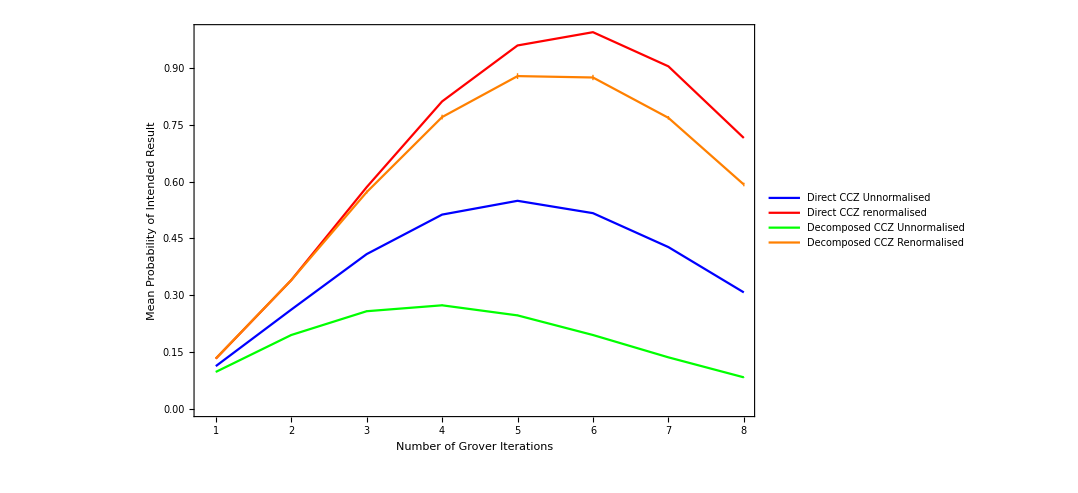

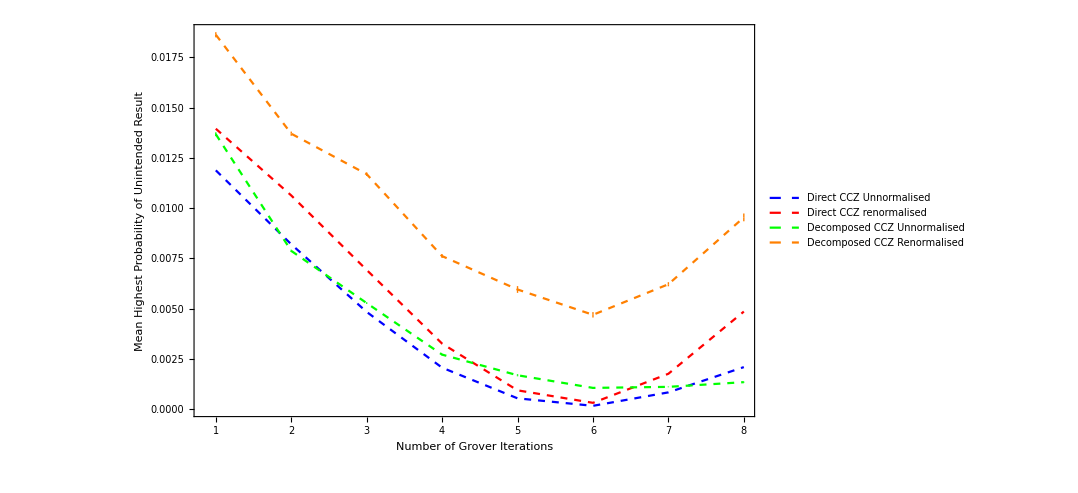

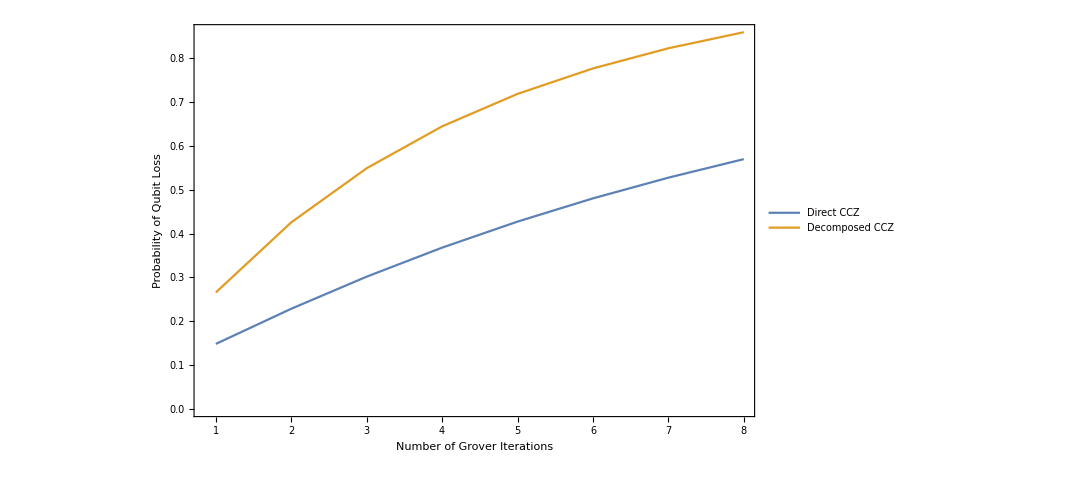

```mathematica
ListLinePlot[{GroverDataUnnormVaryIt,GroverDataRenormVaryIt,GroverDataUnnormVaryIt2Q,GroverDataRenormVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{Blue,Red,Green,Orange},FrameLabel->{"Number of Grover Iterations","Mean Probability of Intended Result"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ Unnormalised","Direct CCZ renormalised","Decomposed CCZ Unnormalised","Decomposed CCZ Renormalised"},{Left,Top}]]
ListLinePlot[{GroverData2ndHighestUnnormVaryIt,GroverData2ndHighestRenormVaryIt,GroverData2ndHighestUnnormVaryIt2Q,GroverData2ndHighestRenormVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Blue,Dashed},{Red,Dashed},{Green,Dashed},{Orange,Dashed}},FrameLabel->{"Number of Grover Iterations"," Mean Highest Probability of Unintended Result"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ Unnormalised","Direct CCZ renormalised","Decomposed CCZ Unnormalised","Decomposed CCZ Renormalised"},{Right,Top}]]
ListLinePlot[{PLossVaryIt,PLossVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],FrameLabel->{"Number of Grover Iterations","Probability of Qubit Loss"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ","Decomposed CCZ"},{Right,Bottom}]]
```

```mathematica
RenormList
```

{0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458396,0.458395,0.458395,0.458395,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458396,0.458396,0.458396,0.458395,0.458395,0.458395,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458396,0.458396,0.458396,0.458395,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396}